# Hilltop Potential Using Professor’s code

First, we are defining some of the constants which with we will work.
Also define a special case, when p = 4.0 and the values of ϕini and ϕend are given in function of this parameter. 
[See notebook of hilltop potential to revise the code of these calculation]
Also it is define the potetial dependent of ϕ

Revise parameters M and μ in the paper.

```mathematica
M:=0.007649235245744417
p:= 4
μ:= 70.0
ϕini := 59.87862053819866
ϕend:= 69.30346456329042
h1:=0.005
V[ϕ_]:= M^4 (1 - (ϕ/μ)^p)
h[ϕ_]:=1/(M^4 p)√3 (-1/(M^4 (-2+p))ϕ^2 (ϕ/μ)^-p (-M^4 (-1+(ϕ/μ)^p))^(3/2) Hypergeometric2F1[1,1/2+2/p,2/p,(ϕ/μ)^p]+1/(M^4 (-2+p))ϕini^2 (ϕini/μ)^-p (-M^4 (-1+(ϕini/μ)^p))^(3/2) Hypergeometric2F1[1,1/2+2/p,2/p,(ϕini/μ)^p])
```

```mathematica
root[t_]:=FindRoot[h[ϕ]-t==0,{ϕ,ϕini}]
ϕsr[t_]:=(ϕ/.First[root[t]])
ϕsrp[t_]:=(ϕsr[t+h1]-ϕsr[t])/h1
```

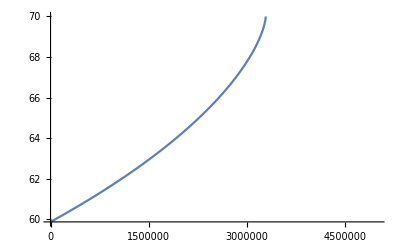

```mathematica
Plot[ϕsr[t],{t,0,0.5*10^7}]
```

```mathematica
ϕsr[3.2277066504825214*^6]
```

69.1646

```mathematica
w=NDSolve[{ϕt''[t]+3Sqrt[1/3((ϕt'[t])^2/2+(1 - (ϕt[t]/μ)^p))] ϕt'[t] +D[V[ϕt[t]],ϕt[t]]==0,ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0]},{ϕt,ϕt'},{t,-3*10^10, 10^10}];
```

NDSolve::ndsz: At t == -11.7453, step size is effectively zero; singularity or stiff system suspected.

```mathematica
ϕ[t_]:=(ϕt/.First[w])[t];
pϕ[t_]:=(ϕt'/.First[w])[t];
ppϕ[t_]:=(ϕt''/.First[w])[t];
pppϕ[t_]:=(ϕt'''/.First[w])[t];
```

```mathematica
ϕ[t]
```

InterpolatingFunction[…][t]

```mathematica
tend=t/.FindRoot[ϕ[t]==ϕend,{t,10^7}]; 
tend
```

InterpolatingFunction::dmval: Input value {1.331×10^10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.05711×10^10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.00361×10^10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-2.18494×10^11} and/or the interpolation grid is insufficient to compute the value.

FindRoot::nlnum: The function value {-69.3035+InterpolatingFunction[{{-11.7453,1.×10^10}},{5,7,2,{992},{4},0,0,0,0,Automatic,«3»},{{-11.7453,-11.7453,-11.7453,«6»,-11.7453,«982»}},{Developer`PackedArrayForm,{0,3,6,9,12,15,18,21,24,27,«983»},{38.3174,1.44705×10^11,-2.56457×10^22,38.3448,1.39927×10^11,-2.39801×10^22,38.3713,1.35455×10^11,-2.24717×10^22,38.397,«2966»}},{Automatic}][-«23»]} is not a list of numbers with dimensions {1} at {t} = {-2.18494×10^11}.

2.42771×10^10

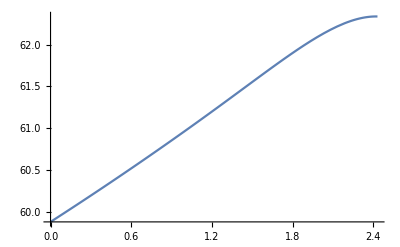

```mathematica
Plot[ϕ[t],{t,0.,2.43 10^10}]
```